```mathematica
src=Import["/home/artem/projects/data_claster/trace1d.txt", "Table"]//Flatten
data=Table[{(0.5  i)/Length[src],src[[i]]/Max[src]},{i,1,Length[src]}];
data[[1,1]] = 0;
```

{0.643568,0.643803,0.642194,0.642184,0.641969,0.641915,0.64183,0.641892,0.639544,0.639669,0.635623,0.635441,0.635278,0.633855,0.633401,0.629019,0.628781,0.628506,0.628414,0.624131,0.623801,0.617846,0.617734,0.617573,0.613571,0.612795,0.612605,0.606953,0.606584,0.606433,0.597617,0.597258,0.595704,0.585818,0.585643,0.577165,0.577026,0.576771,0.556607,0.555816,0.550209,0.54978,0.549412,0.545077,0.54469,0.523272,0.522705,0.513799,0.513156,0.49337,0.472309,0.471836,0.460222,0.459958,0.447564,0.42236,0.413172,0.412398,0.40678,0.405274,0.364277,0.36356,0.342726,0.335531,0.269294,0.230433,0.1949}

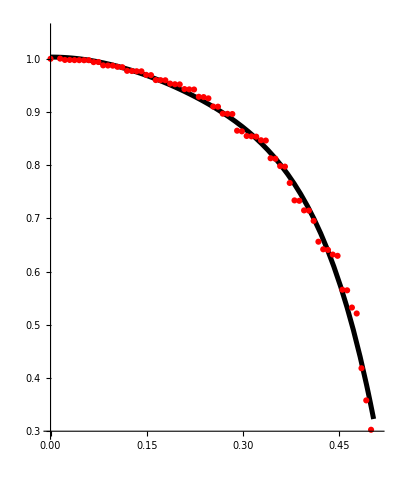

```mathematica
Parabola=Fit[data,{1,x^2,x^4,x^6},x];
Show[Plot[Parabola,{x,0,0.504},PlotStyle->Directive[Black, Thickness[0.009]],PlotRange->{{0,0.51},{0.3,1.05}}, AspectRatio->1.2/1],
ListPlot[data,PlotStyle->Red]]
```